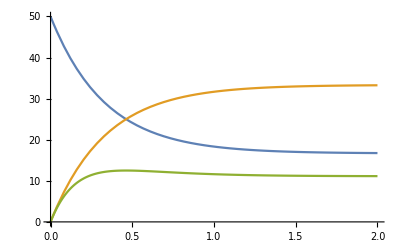

{{18.3262356123},{31.6737643877},{347.460129094},{11.6092173779}}

```mathematica
ClearAll["Global`*"]
(*NOTE: x*x ≠ xsq*)
eqns2={x'[t]==-2*x[t]+y[t],
y'[t]==2*x[t]-y[t],
xsq'[t]==-4*xsq[t]-2xsq[t]+2(x[t]+y[t])x[t]+y[t]+2x[t],
x[0]==50,y[0]==0,xsq[0]==50^2};
sol=DSolve[eqns2,{x,y,xsq},t];
Plot[{x[t]/.sol,y[t]/.sol,xsq[t]-x[t]^2/.sol},{t,0,2}]
N[{x[t]/.sol,y[t]/.sol,xsq[t]/.sol,xsq[t]-x[t]^2/.sol}/.{t->1},12]
```